# Домашняя работа №9 Выполнил Александр Широков, ПМ-1701

## Package

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["MethodSugiyama`"]
```

```mathematica
?"MethodSugiyama`*"
```

```mathematica
graph=GetGraph[10];
```

```mathematica
res=GetDAG[graph];
```

```mathematica
res
```

<|acyclic graph→{1->8,1->10,4->1,4->7,5->2,5->8,5->10,6->1,7->2,9->8,10->9},feedback set→{2->1,2->5,3->6,5->4,7->4,7->6,8->4,8->7,8->9,9->3,9->5,9->6,10->1,10->4,10->7}|>

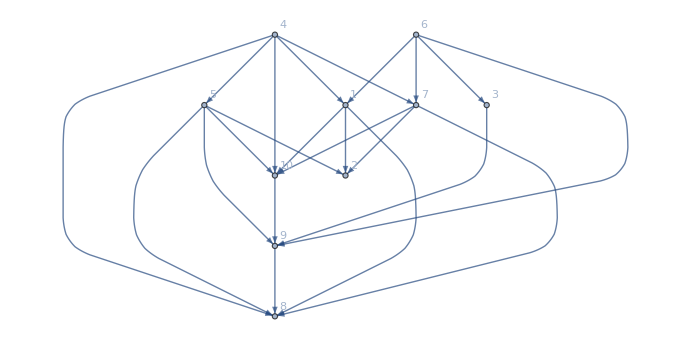

```mathematica
dagGraph=Graph[Union[res["acyclic graph"],Reverse/@res["feedback set"]],VertexLabels->"Name"]
```

## Part I

Сформулировать задачу о распределении вершин по слоям с ограничением на ширину слоя как задачу целочисленного программирования

## Постановка задачи

## Тестовый вариант

Список вершин графа

```mathematica
V=Sort[VertexList[dagGraph]]
```

{1,2,3,4,5,6,7,8,9,10}

Максимальный путь в графе (https://mathematica.stackexchange.com/questions/136277/how-to-find-a-longest-path-which-contains-as-many-vertices)

```mathematica
allPaths=FindPath[dagGraph,#2,#1,Infinity,All]&@@@Subsets[VertexList[dagGraph],{2}]//Apply[Join];
hmax=Length[First[MaximalBy[allPaths,Length@Union@#&]]]
```

5

Пары минимального и максимального слоя

```mathematica
layer1=DeleteDuplicates[MaximalBy[allPaths,Length@Union@#&][[All,1]]];
layerhmax=DeleteDuplicates[MaximalBy[allPaths,Length@Union@#&][[All,-1]]];
hiMin=(Max/@Table[Max[Length/@FindPath[dagGraph,v,ver,Infinity,All]],{ver,V},{v,layer1}])/.{-∞->1};
hiMax=(hmax-Max/@Table[Max[Length/@FindPath[dagGraph,ver,v,Infinity,All]],{ver,V},{v,layerhmax}]+1)/.{∞->hmax};
hMinhMaxPare=Association[Thread[V->Thread[{hiMin,hiMax}]]]
```

<|1→{2,2},2→{3,5},3→{2,3},4→{1,1},5→{2,2},6→{1,1},7→{2,2},8→{5,5},9→{4,4},10→{3,3}|>

Переменные

```mathematica
varsX=Array[x,{Length@V,hmax}];
varXcond=Table[Cases[u,x[a_,e_]/;First[hMinhMaxPare[First[u]⟦1⟧]]≤e≤Last[hMinhMaxPare[First[u]⟦1⟧]]->x[a,e]],{u,varsX}]
varDelta=Array[Φ,1]
varW=Array[W,1]
vars=Join[Flatten@varXcond,varDelta,varW]
```

{{x[1,2]},{x[2,3],x[2,4],x[2,5]},{x[3,2],x[3,3]},{x[4,1]},{x[5,2]},{x[6,1]},{x[7,2]},{x[8,5]},{x[9,4]},{x[10,3]}}

{Φ[1]}

{W[1]}

{x[1,2],x[2,3],x[2,4],x[2,5],x[3,2],x[3,3],x[4,1],x[5,2],x[6,1],x[7,2],x[8,5],x[9,4],x[10,3],Φ[1],W[1]}

```mathematica
α=0.29;
weights={α,1-α}
```

{0.29,0.71}

Целевая функция

```mathematica
objfun=Total[Join[varDelta,varW]*weights]
```

0.71 W[1]+0.29 Φ[1]

Первое ограничение

```mathematica
Total[GatherBy[Flatten@varXcond,Last],{2}]-First@varW
```

{-W[1]+x[1,2]+x[3,2]+x[5,2]+x[7,2],-W[1]+x[2,3]+x[3,3]+x[10,3],-W[1]+x[2,4]+x[9,4],-W[1]+x[2,5]+x[8,5],-W[1]+x[4,1]+x[6,1]}

```mathematica
cond1=Total[GatherBy[Flatten@varXcond,Last],{2}]-First@varW
r1= ConstantArray[{0,-1},Length[cond1]]
```

{-W[1]+x[1,2]+x[3,2]+x[5,2]+x[7,2],-W[1]+x[2,3]+x[3,3]+x[10,3],-W[1]+x[2,4]+x[9,4],-W[1]+x[2,5]+x[8,5],-W[1]+x[4,1]+x[6,1]}

{{0,-1},{0,-1},{0,-1},{0,-1},{0,-1}}

Второе ограничение

```mathematica
cond2=Total[varXcond,{2}]
r2= ConstantArray[{1,0},Length[cond2]]
```

{x[1,2],x[2,3]+x[2,4]+x[2,5],x[3,2]+x[3,3],x[4,1],x[5,2],x[6,1],x[7,2],x[8,5],x[9,4],x[10,3]}

{{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}}

Lambda

```mathematica
lambda=Table[∑_(k=First[hMinhMaxPare[ver]])^Last[hMinhMaxPare[ver]] k*x[ver,k],{ver,V}]
```

{2 x[1,2],3 x[2,3]+4 x[2,4]+5 x[2,5],2 x[3,2]+3 x[3,3],x[4,1],2 x[5,2],x[6,1],2 x[7,2],5 x[8,5],4 x[9,4],3 x[10,3]}

Третье ограничение

```mathematica
cond3=lambda-First@varDelta
r3= ConstantArray[{0,-1},Length[cond3]]
```

{2 x[1,2]-Φ[1],3 x[2,3]+4 x[2,4]+5 x[2,5]-Φ[1],2 x[3,2]+3 x[3,3]-Φ[1],x[4,1]-Φ[1],2 x[5,2]-Φ[1],x[6,1]-Φ[1],2 x[7,2]-Φ[1],5 x[8,5]-Φ[1],4 x[9,4]-Φ[1],3 x[10,3]-Φ[1]}

{{0,-1},{0,-1},{0,-1},{0,-1},{0,-1},{0,-1},{0,-1},{0,-1},{0,-1},{0,-1}}

Четвертое ограничение

```mathematica
cond4=Table[lambda⟦Last[A]⟧-lambda⟦First[A]⟧,{A,EdgeList[dagGraph]}]
r4=ConstantArray[{1,1},Length[cond4]]
```

{-2 x[1,2]+3 x[2,3]+4 x[2,4]+5 x[2,5],-2 x[1,2]+5 x[8,5],-2 x[1,2]+3 x[10,3],-2 x[3,2]-3 x[3,3]+4 x[9,4],2 x[1,2]-x[4,1],-x[4,1]+2 x[5,2],-x[4,1]+2 x[7,2],-x[4,1]+5 x[8,5],-x[4,1]+3 x[10,3],3 x[2,3]+4 x[2,4]+5 x[2,5]-2 x[5,2],-2 x[5,2]+5 x[8,5],-2 x[5,2]+4 x[9,4],-2 x[5,2]+3 x[10,3],2 x[1,2]-x[6,1],2 x[3,2]+3 x[3,3]-x[6,1],-x[6,1]+2 x[7,2],-x[6,1]+4 x[9,4],3 x[2,3]+4 x[2,4]+5 x[2,5]-2 x[7,2],-2 x[7,2]+5 x[8,5],-2 x[7,2]+3 x[10,3],5 x[8,5]-4 x[9,4],4 x[9,4]-3 x[10,3]}

{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}}

Решение задачи

```mathematica
c=Last@CoefficientArrays[objfun,vars]
m = Last@CoefficientArrays[Join[cond1,cond2,cond3,cond4],vars];
b = Join[r1,r2 ,r3,r4];
lu = Join[ConstantArray[{0,1},Length[Flatten@varXcond]],ConstantArray[{0,Infinity},2]];
domain = Join[ConstantArray[Integers,Length[Flatten@varXcond]],ConstantArray[Integers,2]];
solution = Quiet[LinearProgramming[c,m,b,lu,domain]]
```

SparseArray[…]

{1,1,0,0,0,1,1,1,1,1,1,1,1,5,3}

```mathematica
Print[Dimensions[c],Dimensions[m],Dimensions[b],Dimensions[lu],Dimensions[domain]];
```

{15}{47,15}{47,2}{15,2}{15}

```mathematica
layers=GatherBy[SortBy[Pick[Flatten@varXcond,solution⟦;;-3⟧,1],Last],Last]⟦All,All,1⟧
```

{{4,6},{1,5,7},{2,3,10},{9},{8}}

## Реализация

```mathematica
minimizeW[DAG_,α_,β_]:=Module[{V=Sort[VertexList[DAG]],allPaths,hmax,layer1,layerhmax,hiMax,hiMin,hMinhMaxPare,varsX,varXcond,varDelta,varW,vars,weights,objfun,cond1,r1,cond2,r2,lambda,cond3,r3,cond4,r4,c,m,b,lu,domain,solution,layers},
Clear[x,a,e,u,Φ,W];
allPaths=FindPath[DAG,#2,#1,Infinity,All]&@@@Subsets[VertexList[DAG],{2}]//Apply[Join];
hmax=Length[First[MaximalBy[allPaths,Length@Union@#&]]];
layer1=DeleteDuplicates[MaximalBy[allPaths,Length@Union@#&][[All,1]]];
layerhmax=DeleteDuplicates[MaximalBy[allPaths,Length@Union@#&][[All,-1]]];
hiMin=(Max/@Table[Max[Length/@FindPath[DAG,v,ver,Infinity,All]],{ver,V},{v,layer1}])/.{-∞->1};
hiMax=(hmax-Max/@Table[Max[Length/@FindPath[DAG,ver,v,Infinity,All]],{ver,V},{v,layerhmax}]+1)/.{∞->hmax};
hMinhMaxPare=Association[Thread[V->Thread[{hiMin,hiMax}]]];
varsX=Array[x,{Length@V,hmax}];
varXcond=Table[Cases[u,x[a_,e_]/;First[hMinhMaxPare[First[u]⟦1⟧]]≤e≤Last[hMinhMaxPare[First[u]⟦1⟧]]->x[a,e]],{u,varsX}];
varDelta=Array[Φ,1];
varW=Array[W,1];
vars=Join[Flatten@varXcond,varDelta,varW];
weights={α,β};
objfun=Total[Join[varDelta,varW]*weights];
cond1=Total[GatherBy[Flatten@varXcond,Last],{2}]-First@varW;
r1= ConstantArray[{0,-1},Length[cond1]];
cond2=Total[varXcond,{2}];
r2= ConstantArray[{1,0},Length[cond2]];
lambda=Table[∑_(k=First[hMinhMaxPare[ver]])^Last[hMinhMaxPare[ver]] k*x[ver,k],{ver,V}];
cond3=lambda-First@varDelta;
r3= ConstantArray[{0,-1},Length[cond3]];
cond4=Table[lambda⟦Last[A]⟧-lambda⟦First[A]⟧,{A,EdgeList[DAG]}];
r4=ConstantArray[{1,1},Length[cond4]];
c=Last@CoefficientArrays[objfun,vars];
m = Last@CoefficientArrays[Join[cond1,cond2,cond3,cond4],vars];
b = Join[r1,r2 ,r3,r4];
lu = Join[ConstantArray[{0,1},Length[Flatten@varXcond]],ConstantArray[{0,Infinity},2]];
domain = Join[ConstantArray[Integers,Length[Flatten@varXcond]],ConstantArray[Integers,2]];
Print[Dimensions[c],Dimensions[m],Dimensions[b],Dimensions[lu],Dimensions[domain]];
solution = Quiet[LinearProgramming[c,m,b,lu,domain]];
Print[solution[[-2;;]]];
layers=GatherBy[SortBy[Pick[Flatten@varXcond,solution[[;;-3]],1],Last],Last][[All,All,1]]
]
```

```mathematica
minimizeW[dagGraph,0,10]
```

{15}{47,15}{47,2}{15,2}{15}

{5,3}

{{4,6},{1,5,7},{2,3,10},{9},{8}}

### Test

α-количество слоёв, β-ширина слоёв

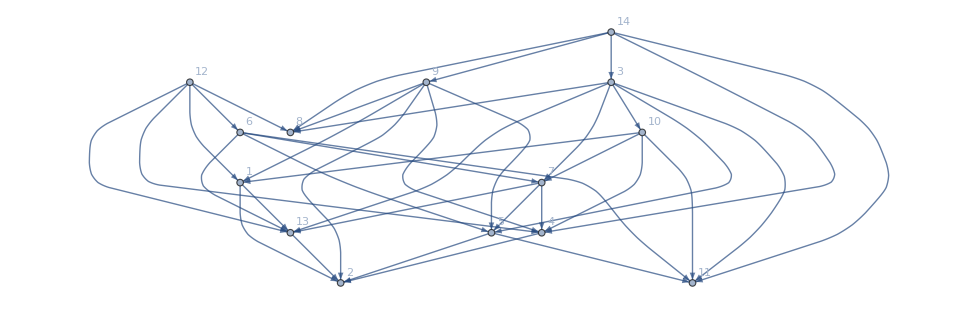

{23}{72,23}{72,2}{23,2}{23}

{6,3}

{{12,14},{3,9},{6,8,10},{1,7},{4,5,13},{2,11}}

```mathematica
test=GetDAG[GetGraph[14]];
y=Graph[Union[test["acyclic graph"],Reverse/@test["feedback set"]],VertexLabels->"Name"];
y
minimizeW[y,1,1]
```

## Part II

Реализовать алгоритм для подсчета числа пересечений ребер для многослойного иерархического графа без длинных ребер с заданным порядком вершин на слоях (через проверку пересечений всех пар ребер для ребер двухслойных подграфов; прямой алгоритм с использованием XOR).

## Test

```mathematica
Clear[isPairOfEdgesCrossing]
isPairOfEdgesCrossing[{e1_,e2_},layers_]:=Module[{res},
	res=If[e1⟦1⟧ === e2⟦1⟧ ||e1⟦2⟧ ===e2⟦2⟧||e1⟦1,1⟧<e2⟦1,1⟧ ||e2⟦1,1⟧<e1⟦1,1⟧,0,
			Boole[Xor[Flatten[Position[layers,e1⟦1⟧]]⟦2⟧ < Flatten[Position[layers,e2⟦1⟧]]⟦2⟧,Flatten[Position[layers,e1⟦2⟧]]⟦2⟧ < Flatten[Position[layers,e2⟦2⟧]]⟦2⟧]]];Print[{e1,e2},res];res]
```

Будем тестировать на данном тестовом примере (придумал).

Всего должно быть 4 ребра. Идея следующая: если родители ребер равны, или дети равны у ребер соответствующих, или ребра на разных уровнях, то ноль, иначе - применяем XOR

```mathematica
edges={4->8,6->7,8->9,7->10,6->1,1->9,8->10};
layers={{4,6},{7,8,1},{9,10}};
newnames=MapIndexed[v[#2⟦1⟧,#1]&,layers,{2}];
rules=MapThread[Rule,{Flatten@layers,Flatten@newnames}];
arcsWithLongConnections=EdgeList@edges/.rules;
sub=Subsets[arcsWithLongConnections,{2}];
```

```mathematica
amountOf=Total@Table[isPairOfEdgesCrossing[s,newnames],{s,sub}]
```

{v[1,4]->v[2,8],v[1,6]->v[2,7]}1

{v[1,4]->v[2,8],v[2,8]->v[3,9]}0

{v[1,4]->v[2,8],v[2,7]->v[3,10]}0

{v[1,4]->v[2,8],v[1,6]->v[2,1]}0

{v[1,4]->v[2,8],v[2,1]->v[3,9]}0

{v[1,4]->v[2,8],v[2,8]->v[3,10]}0

{v[1,6]->v[2,7],v[2,8]->v[3,9]}0

{v[1,6]->v[2,7],v[2,7]->v[3,10]}0

{v[1,6]->v[2,7],v[1,6]->v[2,1]}0

{v[1,6]->v[2,7],v[2,1]->v[3,9]}0

{v[1,6]->v[2,7],v[2,8]->v[3,10]}0

{v[2,8]->v[3,9],v[2,7]->v[3,10]}1

{v[2,8]->v[3,9],v[1,6]->v[2,1]}0

{v[2,8]->v[3,9],v[2,1]->v[3,9]}0

{v[2,8]->v[3,9],v[2,8]->v[3,10]}0

{v[2,7]->v[3,10],v[1,6]->v[2,1]}0

{v[2,7]->v[3,10],v[2,1]->v[3,9]}1

{v[2,7]->v[3,10],v[2,8]->v[3,10]}0

{v[1,6]->v[2,1],v[2,1]->v[3,9]}0

{v[1,6]->v[2,1],v[2,8]->v[3,10]}0

{v[2,1]->v[3,9],v[2,8]->v[3,10]}1

4

## Реализация

```mathematica
resdummies=AddDummyVertices[Composition[GetLayering,GetDAG][GetGraph[10]],ApproachOption->"Cut"]
```

<|acyclic graph→{1->2,1->4,1->7,3->2,6->3,6->4,6->5,7->3,8->3,8->6},feedback set→{1->9,2->3,2->6,2->8,2->9,3->10,4->1,4->10,5->1,5->9,7->1,7->5,7->9,10->8},graph with dummies→{1->4,3->2,6->4,6->5,7->3,8->6,9->1,10->4,1->5,5->7,8->10,1->11,11->12,12->13,13->2,1->14,14->7,6->15,15->16,16->3,8->17,17->18,18->19,19->3,6->11,10->11,9->10,10->20,20->21,21->3,9->22,22->5,9->23,23->24,24->7},layers with dummies→{{8,9},{1,6,10,17,22,23},{4,5,11,14,15,18,20,24},{7,12,16,19,21},{3,13},{2}},first dummy→11|>

```mathematica
Clear[isCrossing]
isCrossing[{e1_,e2_},layers_]:=If[e1⟦1⟧ === e2⟦1⟧ || e1⟦2⟧ === e2⟦2⟧||e1⟦1,1⟧<e2⟦1,1⟧ ||e2⟦1,1⟧<e1⟦1,1⟧,0,
			Boole[Xor[Flatten[Position[layers,e1⟦1⟧]]⟦2⟧ < Flatten[Position[layers,e2⟦1⟧]]⟦2⟧,Flatten[Position[layers,e1⟦2⟧]]⟦2⟧ <Flatten[ Position[layers,e2⟦2⟧]]⟦2⟧]]];
```

```mathematica
amountOfCrossingEdges[GDum_]:=Module[{layers=GDum["layers with dummies"],edges=GDum["graph with dummies"],newnames,rules,arcsWithLongConnections,sub,amountOf},
newnames=MapIndexed[v[#2⟦1⟧,#1]&,layers,{2}];
rules=MapThread[Rule,{Flatten@layers,Flatten@newnames}];
arcsWithLongConnections=EdgeList@edges/.rules;sub=Subsets[arcsWithLongConnections,{2}];amountOf=Total@Table[isCrossing[s,newnames],{s,sub}]]
```

```mathematica
amountOfCrossingEdges[resdummies]
```

34

## Part III

Для данного примера решим.

```mathematica
edge={1->1,2->1,2->2,2->3,2->4,3->3,4->4}
```

{1→1,2→1,2→2,2→3,2→4,3→3,4→4}

```mathematica
Cases[Subsets[edge,{2}],{i_->j_,k_->l_}/;i<j ->f[i,j,k,l]]
```

{f[2,3,2,4],f[2,3,3,3],f[2,3,4,4],f[2,4,3,3],f[2,4,4,4]}

```mathematica
Clear[c]
```

```mathematica
varc=Table[f[s⟦1,1⟧,s⟦1,2⟧,s⟦2,1⟧,s⟦2,2⟧],{s,Subsets[edge,{2}]}]
```

{f[1,1,2,1],f[1,1,2,2],f[1,1,2,3],f[1,1,2,4],f[1,1,3,3],f[1,1,4,4],f[2,1,2,2],f[2,1,2,3],f[2,1,2,4],f[2,1,3,3],f[2,1,4,4],f[2,2,2,3],f[2,2,2,4],f[2,2,3,3],f[2,2,4,4],f[2,3,2,4],f[2,3,3,3],f[2,3,4,4],f[2,4,3,3],f[2,4,4,4],f[3,3,4,4]}

```mathematica
Cases[varc,f[i_,j_,k_,l_]/;i<j&&k<l&&i<k&&j≠l->f[i,j,k,l]]
```

{}

После этого я не понял, как создаются переменные

1. c_(i,j,k,l) обозначает пересекаются ли ребра (i,j) и (k,l), когда i<j, k<l, i<k и j ≠ l.